# Interlude 2

## Power Series

## Section I2.2

### Exercise I2.2.3

#### (sin(x))/x at x==0

```mathematica
Series[Sin[x],{x,0,2}]
```

x+O[x]^3

```mathematica
?SeriesCoefficient
```

SeriesCoefficient[series,n] finds the coefficient of the n^th-order term in a power series in the form generated by Series. 
SeriesCoefficient[f,{x,x_0,n}] finds the coefficient of (x-x_0)^n in the expansion of f about the point x=x_0.
SeriesCoefficient[f,{x,x_0,n_x},{y,y_0,n_y},…] finds a coefficient in a multivariate series.

```mathematica
SeriesCoefficient[Sin[x],{x,0,n}]
```

Piecewise[{{(ⅈ ⅈ^n (-1+(-1)^n))/(2 n!), n≥0}, {0, True}}]

```mathematica
Sum[(-x^2)^k/(2k+1)!,{k,0,Infinity}]
```

Sin[x]/x

#### (exp(x)-1)/x at x==0

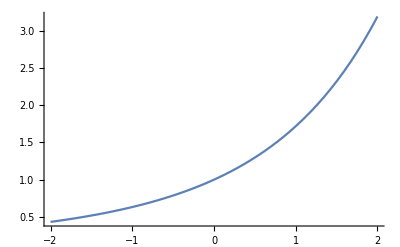

```mathematica
Plot[(Exp[x]-1)/x,{x,-2,2}]
```

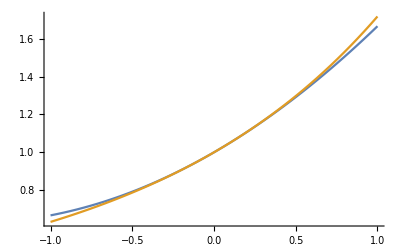

```mathematica
Plot[{1+x/2!+x^2/3!,(Exp[x]-1)/x},{x,-1,1}]
```

```mathematica
Sum[x^(k-1)/k!,{k,1,Infinity}]
```

(-1+ⅇ^x)/x

### Exercise I2.2.8

#### Definitional issues

```mathematica
Sum[x^k/(k*k!),{k,1,Infinity}]
```

-EulerGamma-Gamma[0,-x]-Log[-x]

Stoppel defines the exponential integral function as

x==∫_0^x (exp(t)-1)/t ⅆt

Mathematica defines it as

x==∫_(-∞)^x (exp(t))/t ⅆt

Proof

```mathematica
D[ExpIntegralEi[x],x]
```

ⅇ^x/x

```mathematica
ExpIntegralEi[0]
```

-∞

```mathematica
Integrate[Exp[t]/t,{t,-Infinity,x}]
```

ConditionalExpression[ExpIntegralEi[x],Im[x]≠0||Re[x]<0]

#### Workarounds

```mathematica
Series[Integrate[(Exp[t]-1)/t,{t,0,x},Assumptions->{x<0}]//Evaluate,{x,0,3}]
```

-2 ⅈ π+x+x^2/4+x^3/18+O[x]^4

```mathematica
Sum[x^k/(k*k!),{k,1,3}]+O[x]^4
```

x+x^2/4+x^3/18+O[x]^4

```mathematica
Series[ExpIntegralEi[x],{x,0,3}]
```

-ⅈ (π Floor[(π+Arg[x])/(2 π)]+(ⅈ (EulerGamma+Log[x])+ⅈ x+(ⅈ x^2)/4+(ⅈ x^3)/18+O[x]^4))

```mathematica
D[ExpIntegralEi[x],x]
```

ⅇ^x/x

```mathematica
Limit[ExpIntegralEi[x]-Log[x],x->0]
```

EulerGamma

```mathematica
Integrate[1/t,{t,-1,x}]
```

ConditionalExpression[-ⅈ π+Log[x],Re[x]≤0||x∉Reals]

```mathematica
NIntegrate[(Exp[x]-1)/x,{x,0,-2}]
```

-1.31926

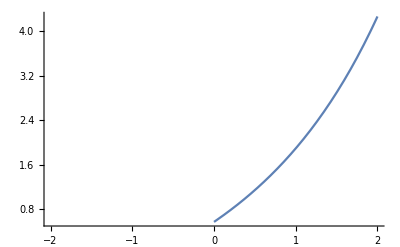

```mathematica
Plot[ExpIntegralEi[x]-Log[x],{x,-2,2}]
```

```mathematica
FullSimplify[
Series[Integrate[(Exp[t]-1)/t,{t,0,x},Assumptions->{0<x,x∈Reals}]//Evaluate,{x,0,3}],
0<x]
```

x+x^2/4+x^3/18+O[x]^4

```mathematica
Sum[x^k/(k*k!),{k,1,3}]+O[x]^4
```

x+x^2/4+x^3/18+O[x]^4

```mathematica
intPos=Integrate[(Exp[t]-1)/t,{t,0,x},Assumptions->{0<x,x∈Reals}]
```

-EulerGamma+ExpIntegralEi[x]-Log[x]

```mathematica
intNeg=Integrate[(Exp[t]-1)/t,{t,0,x},Assumptions->{x<0,x∈Reals}]
```

-EulerGamma-ⅈ π+CoshIntegral[x]-Log[-x]+SinhIntegral[x]

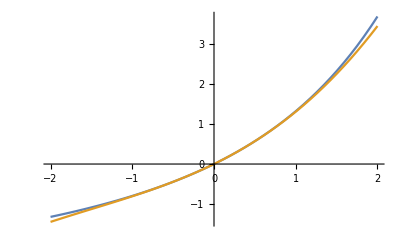

```mathematica
Plot[{
Piecewise[{{intPos,0<x},{intNeg,x<0}}],

Sum[x^k/(k*k!),{k,1,3}]
},{x,-2,2}]
```

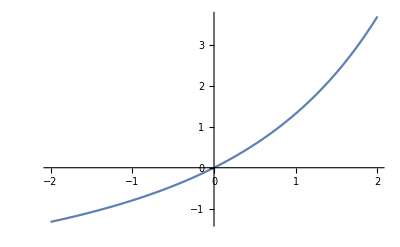

```mathematica
Plot[Sum[x^k/(k*k!),{k,1,Infinity}]//Evaluate,{x,-2,2}]
```

```mathematica
Reduce[Sum[x^k/(k*k!),{k,1,Infinity},Assumptions->{x∈Reals,x<0}]==Integrate[(Exp[t]-1)/t,{t,0,x},Assumptions->{x∈Reals,x<0}]]
```

CoshIntegral[x]==ⅈ π-Gamma[0,-x]-SinhIntegral[x]

It looks like there’s a confusion around branch cuts.

### Exercise I2.2.9

```mathematica
?PolyLog
```

PolyLog[n,z] gives the polylogarithm function Li_n(z).
PolyLog[n,p,z] gives the Nielsen generalized polylogarithm function S_(n,p)(z).

```mathematica
PolyLog[2,x]
```

PolyLog[2,x]

```mathematica
Integrate[-Log[1-t]/t,{t,0,x}]
```

ConditionalExpression[PolyLog[2,x],Im[x]≠0||Re[x]≤1]

```mathematica
logSeries=Series[Log[1+t],{t,0,3}]
```

t-t^2/2+t^3/3+O[t]^4

```mathematica
InputForm[logSeries]
```

SeriesData[t, 0, {1, -1/2, 1/3}, 1, 4, 1]

```mathematica
negated=-logSeries/.HoldPattern[SeriesData[v_,0,coeffs_,min_,max_,den_]]:>SeriesData[v,0,coeffs*(-1)^Range[min,max-1],min,max,den]
```

t+t^2/2+t^3/3+O[t]^4

```mathematica
negated/t
```

1+t/2+t^2/3+O[t]^3

```mathematica
Integrate[negated/t,{t,0,x}]
```

x+x^2/4+x^3/9

```mathematica
Series[PolyLog[2,x],{x,0,3}]
```

x+x^2/4+x^3/9+O[x]^4

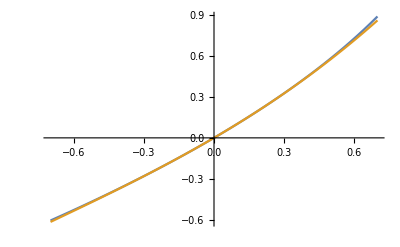

```mathematica
Plot[{PolyLog[2,x],Series[PolyLog[2,x],{x,0,3}]//Normal//Evaluate},{x,-0.7,0.7}]
```

### Section I2.3

```mathematica
Limit[Csc[x]*(Exp[x]-1),x->0]
```

1

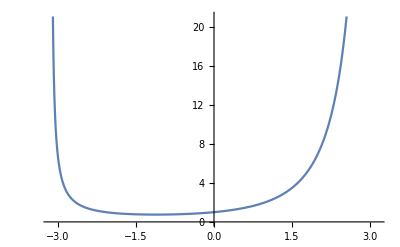

```mathematica
Plot[Csc[x]*(Exp[x]-1),{x,-Pi,Pi}]
```

```mathematica
ClearAll[f,z,a]
```

```mathematica
?SeriesData
```

SeriesData[x,x_0,{a_0,a_1,…},n_min,n_max,den] represents a power series in the variable x about the point x_0. The a_i are the coefficients in the power series. The powers of (x-x_0) that appear are n_min/den, (n_min+1)/den, …, n_max/den.

```mathematica
SeriesData[z,a,{a[1]},-1,0,1]
```

a[1]/(z-a)+O[z-a]^0

```mathematica
f[z_]:=SeriesData[z,a,{a[1]},1,2,1]
```

```mathematica
f[z]
```

a[1] (z-a)+O[z-a]^2

```mathematica
f'[z]/f[z]
```

1/(z-a)+O[z-a]^0

### Exercise I2.3.3

```mathematica
ClearAll[f,z,a,𝒩]
```

```mathematica
f[z_]:=SeriesData[z,a,{a[𝒩]},𝒩,𝒩+1,1]
```

```mathematica
f[z]
```

SeriesData::sdatn: Order specification 𝒩 in SeriesData[z,a,{a[𝒩]},𝒩,1+𝒩,1] is not a machine-sized integer.

SeriesData[z,a,{a[𝒩]},𝒩,1+𝒩,1]

```mathematica
ClearAll[f,z,a,𝒩]
```

```mathematica
f[z_]:=a[𝒩](z-a)^𝒩
```

```mathematica
ClearAll[f,z,a,𝒩]
```

Time to do it the “hard” way.

f(z)==a_𝒩 (z-a)^𝒩+O((z-a)^(𝒩+1))

f'(z)==𝒩 a_𝒩 (z-a)^(𝒩-1)+O((z-a)^𝒩)

(f'(z))/(f(z))==𝒩/(z-a)+O(1)

```mathematica
?Residue
```

Residue[expr,{z,z_0}] finds the residue of expr at the point z=z_0.

```mathematica
Residue[𝒩/(z-a),{z,a}]
```

𝒩

```mathematica
Residue[D[Log[Subscript[a, 𝒩](z-a)^𝒩],z],{z,a}]
```

𝒩

## Section I2.4

### Exercise 1.2.10 Redux

```mathematica
ClearAll[f,n,x]
```

```mathematica
f[n_]:=x^n
```

```mathematica
f[1]
```

x

```mathematica
f[2]
```

x^2

```mathematica
DifferenceDelta[f[n],n]
```

(-1+x) x^n

```mathematica
DifferenceDelta[f[n],n]
```

(-1+x) x^n

∆_n f(n)==(x-1) f(n)

f(n)==(∆_n f(n))/(x-1)

```mathematica
Sum[f[n],n]
```

x^n/(-1+x)

∑_n f(n)==(f(n))/(x-1)

### Exercise I2.4.1

(1-x)(1+x+x^2++x^n) | == | 1+((1x-x1))+((1 x^2-xx))+((1 x^3-x x^2))++((1 x^n-x x^(n-1)))-x x^n
  | == | 1-x^(n+1)

Also straightforward using induction a little more explicitly.

```mathematica
Expand[(1-x^(n+1))/(1-x)]
```

1/(1-x)-x^(1+n)/(1-x)

```mathematica
Together[1/(1-x)+x^(n+1)]
```

(-1-x^(1+n)+x^(2+n))/(-1+x)

```mathematica
%+%%-1/(1-x)
```

-x^(1+n)/(1-x)+(-1-x^(1+n)+x^(2+n))/(-1+x)

```mathematica
Together[%]
```

(-1+x^(2+n))/(-1+x)

### Exercise I2.4.1

```mathematica
1/(1-x)/.x->1/10
```

10/9

```mathematica
Sum[1/10^k,{k,0,Infinity}]
```

10/9

## Section I2.6

### Exercise 1.2.12 Redux

```mathematica
FactorialPower[k-1,-2]//FunctionExpand
```

2/(k (1+k))

```mathematica
Sum[FactorialPower[k-1,-2],k]
```

-1/k

```mathematica
FactorialPower[k-1,-1]
```

1/k

```mathematica
DifferenceDelta[1/k,k]
```

-1/(k (1+k))

∑_(1≤k<n+1) 2 (k-1)^UnderBar[-2]==-2/(n+1)-(-2/1)==2 (1-1/(n+1))

I must have done this before....

### Exercise I2.6.2

```mathematica
Limit[Sum[2/(k*(k+1)),{k,1,n}]//Evaluate,n->Infinity]
```

2

```mathematica
Sum[k*(k+1)/2,{k,1,n}]
```

1/6 n (1+n) (2+n)

```mathematica
FactorialPower[k-1,-3]//FunctionExpand
```

1/(k (1+k) (2+k))

```mathematica
Sum[FactorialPower[k,p],k]
```

FactorialPower[k,1+p]/(1+p)

```mathematica
Sum[6*FactorialPower[k-1,-3],k]
```

-3/(k (1+k))

```mathematica
FactorialPower[k-1,-2]/-2
```

-1/2 FactorialPower[-1+k,-2]

```mathematica
%//FunctionExpand
```

-1/(2 k (1+k))

∑_(1≤k<n+1) 6 (k-1)^UnderBar[-3]==-3/((n+1)(n+2))-(-3/(1×2))==3/2 (1-2/((n+1)(n+2)))

```mathematica
summed=Sum[6*FactorialPower[k-1,-3],{k,1,n}]//FunctionExpand
```

-3/2 (-1+6/((1+n) (2+n) (3+n))+(2 n)/((1+n) (2+n) (3+n)))

```mathematica
Simplify[summed==(3/2)(1-2/((n+1)(n+2)))]
```

True

```mathematica
Sum[6*FactorialPower[k-1,-3],{k,1,Infinity}]
```

3/2

### Exercise I2.6.3

#### 1. Induction on 𝒩

```mathematica
With[{𝒩=1},
{1-1/(2𝒩),1/(𝒩+1)}]
```

{1/2,1/2}

```mathematica
ClearAll[compare];
Attributes[compare]=Listable;
compare[𝒩_Integer?Positive]:=
{Sum[(-1)^(n-1)/n,{n,1,2*𝒩}],Sum[1/n,{n,𝒩+1,2*𝒩}]};
```

```mathematica
compare[Range[4]]
```

{{1/2,1/2},{7/12,7/12},{37/60,37/60},{533/840,533/840}}

When we go from 𝒩 to 𝒩+1, on the left-hand side we add

1/(2 𝒩+1)-1/(2 𝒩+2)

“at the end”, while on the right we add

1/(2 𝒩+1)+1/(2 𝒩+2)

“at the end” and subtract

1/(𝒩+1)

“at the beginning”. In

```mathematica
Together[1/(2 𝒩+1)-1/(2 𝒩+2)]
```

1/(2 (1+𝒩) (1+2 𝒩))

```mathematica
Together[1/(2𝒩+1)+1/(2𝒩+2)]
```

(3+4 𝒩)/(2 (1+𝒩) (1+2 𝒩))

```mathematica
Together[%-1/(𝒩+1)]
```

1/(2 (1+𝒩) (1+2 𝒩))

These are equal, so we’re done.

#### 2. Harmonic numbers

We have

∑_(n=𝒩+1)^(2 𝒩) 1/n==2 𝒩-𝒩

```mathematica
HarmonicNumber[8]-HarmonicNumber[4]
```

533/840

```mathematica
Sum[1/n,{n,𝒩+1,2𝒩}]==HarmonicNumber[2𝒩]-HarmonicNumber[𝒩]//FunctionExpand
```

True

#### 3. Using (3.3)

We have

n==log(n)+ℽ+O(1/n)

Substituing in, this gives

2n-n==log(2n)-log(n)+O(1/n)=log((2n)/n)+O(1/n)=log(2)+O(1/n)

As n → ∞, this goes to log(2).

### Exercise I2.6.12

```mathematica
?RectangleChart
```

RectangleChart[{{x_1,y_1},{x_2,y_2},…}] makes a rectangle chart with bars of width x_i and height y_i. 
RectangleChart[{…,w_i[{x_i,y_i},…],…,w_j[{x_i,y_j},…],…}] makes a rectangle chart with bar features defined by the symbolic wrappers w_k.
RectangleChart[{data_1,data_2,…}] makes a rectangle chart from multiple datasets data_i.

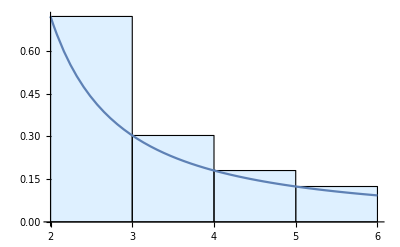

```mathematica
Show[
Plot[1/(x*Log[x]),{x,2,5},AxesOrigin->{2,0}],
Graphics[{LightBlue,EdgeForm[Black],Table[Rectangle[{n,0},{n+1,1/(n*Log[n])}],{n,2,5}]},AxesOrigin->{2,0},PlotRange->{{0,All},{0,All}}],

Plot[1/(x*Log[x]),{x,2,6}],
PlotRange->All
]
```

```mathematica
Integrate[1/(x*Log[x]),x]
```

Log[Log[x]]

```mathematica
Integrate[1/(x*Log[x]),{x,2,𝒩},Assumptions->{2<𝒩}]
```

Log[Log[𝒩]/Log[2]]